## Basics

Nick’s to-do list:
Maybe tweak Lattice[] vertex placement so that connected vertices are closer together

Mathematica basics:
Shift+Enter to evaluate
Hover over a function to get more info on it, and a link to the documentation
When you evaluate something, click “Yes” to automatically evaluate all initialization cells
	i.e. The gray cells, which are all the functions I wrote.
	Ctrl+8 to turn a cell into an initialization cell (do this if you define a new function)

Warning:
Remember that these computations are very exponential in both space and time, i.e. WedgeCongruences has to manage 2^(n
k) subsets where n is the size of the ground set and k is the wedge power, and all of these show up in its output. Big. So if you do a time-intensive computation, don’t just immediately try running VisualizeCongruences[] because Mathematica may crash. Instead, at least save the congruence classes to a .txt file first.

Weird error: don’t use the variable name “Ground”, since that is a function I defined
Also don’t use “I”, “E”, “N” since those are built-in things (unless you define them as local variables in a Module[]...)

## Functions

## General

#### Debug

Two useful functions for when you’re debugging another function, or to easily make a function print/echo things if you tell it to

```mathematica
PrintDebug[debug_,x___]:=If[debug,Print[x]];
```

```mathematica
EchoDebug[debug_,x___]:=If[debug,Echo[x],x];
```

Examples:

```mathematica
PrintDebug[False,"a"]
```

```mathematica
EchoDebug[True,"Thing","Label"]
```

Label Thing

Thing

```mathematica
debug=True;
Do[PrintDebug[debug,i],{i,1,3}]
```

1

2

3

The function defined below has an optional “debug” parameter that defaults to False. Set it to True if you want the extra outputs.

```mathematica
example1[a_,b_,c_,debug_:False]:=Module[{},
PrintDebug[debug,"Now it's gonna echo some things"];
EchoDebug[debug,a^2,"a^2"];
EchoDebug[debug,b^2,"b^2"];
a+b+c
]
```

```mathematica
example1[3,2,1,True]
```

Now it's gonna echo some things

a^2 9

b^2 4

6

Here’s a fancy version showing the basics of options patterns (like how in Plot[] you can set Range→whatever)
I don’t usually use this, but if you ever have complicated code that can have tons of optional inputs but usually just takes default values, this might be a good idea

```mathematica
example2[a_,b_,c_,OptionsPattern[{DebugMode->False}]]:=Module[{debug},
debug=OptionValue[DebugMode];
PrintDebug[debug,"Now it's gonna echo some things"];
EchoDebug[debug,a^2,"a^2"];
EchoDebug[debug,b^2,"b^2"];
a+b+c
]
```

```mathematica
example2[3,2,1,DebugMode->True]
```

Now it's gonna echo some things

a^2 9

b^2 4

6

#### TimeToString

Helps when giving time estimates
It’s also cool if you have the program send you an SMS when it finishes running, with the total time in the message

Time given in seconds

```mathematica
TimeToString[t_]:=Which[
StringQ[t],
t,
t<60,
ToString[Round[t,0.01]]~~" seconds",
t<3600,
ToString[Round[t/60,0.01]]~~" minutes",
True,
ToString[Round[t/3600,0.01]]~~" hours"
]
```

```mathematica
t=12345;
SendMessage["SMS","Code finished running, took "~~TimeToString[t]~~"."]
```

## Matroids

I represent matroids in terms of bases, ie. as the tuple {E,B} where E is the ground set (as a list) and B is a list of bases (B ⊆ 2^E)

### Matroid Construction

#### UniformMatroid

Constructs the uniform matroid U_(d,n)

```mathematica
UniformMatroid[d_,n_Integer]:={Range[n],Subsets[Range[n],{d}]}
```

```mathematica
UniformMatroid[2,4]
```

{{1,2,3,4},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}}

If the user wants to specify the ground set,

```mathematica
UniformMatroid[d_,ground_List]:={ground,Subsets[ground,{d}]}
```

So in this example, the ground set is all pairs of numbers from {1,2,3,4}

```mathematica
UniformMatroid[2,Subsets[Range[4],{2}]]
```

{{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}},{{{1,2},{1,3}},{{1,2},{1,4}},{{1,2},{2,3}},{{1,2},{2,4}},{{1,2},{3,4}},{{1,3},{1,4}},{{1,3},{2,3}},{{1,3},{2,4}},{{1,3},{3,4}},{{1,4},{2,3}},{{1,4},{2,4}},{{1,4},{3,4}},{{2,3},{2,4}},{{2,3},{3,4}},{{2,4},{3,4}}}}

#### GraphicMatroid

Constructs the graphic matroid corresponding to a graph (or a set of edges)
Optional parameter “echo” if the user wants to see the graph
Improvement: optimize how it finds all spanning trees

```mathematica
GraphicMatroid[G_,echo_:False]:=Module[{edges,numberingRule,B},

(*Finds the edges; requires figuring out if a graph or edge list was supplied*)
edges=If[GraphQ@G,EdgeList@G,G];

(*Numbers them automatically*)
numberingRule=Table[edges[[i]]->i,{i,1,Length@edges}];

(*Outputs the graph (if desired)*)
If[echo,Echo[Graph[edges,EdgeLabels->numberingRule],"Graph"]];

(*Determines the minimum spanning trees, which are the bases of our matroid*)
(*First finds a spanning tree, to figure out what size the bases are*)
(*Then selects all acyclic subsets of edges with that size (could probably be made more efficient)*)
(*Finally, assigns numbers to the edges*)
B=EdgeList/@Select[
Graph/@Subsets[edges,{EdgeCount@FindSpanningTree@G}]
,AcyclicGraphQ
]/.numberingRule;

(*Returns the matroid*)
(*The ground set is just the*)
{Range[Length@edges],B}

];
```

#### DualMatroid

Constructs the dual matroid

```mathematica
DualMatroid[M_]:=Module[{E,B},
{E,B}=M;
(*For each basis, takes the complement in E*)
(*The Reverse[] just makes sure the new list of bases is sorted*)
{E,Reverse[Complement[E,#]&/@B]}
]
```

```mathematica
DualMatroid[UniformMatroid[2,5]]
```

{{1,2,3,4,5},{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}}

#### MK4

A good graphic matroid.
Giansiracusa^2 (A Grassman Algebra for Matroids) uses this one for examples (see examples 4.3.2, 6.1.5), so I decided to save it for easy use.
It’s useful since it’s a small nonuniform matroid.

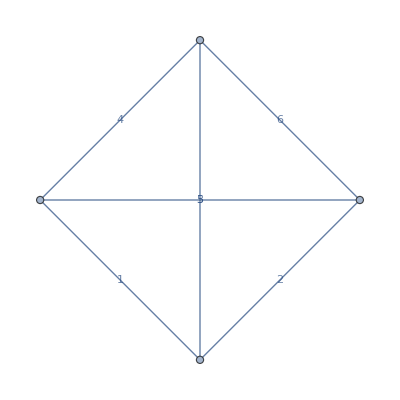
Graph -Graphics-

{{1,2,3,4,5,6},{{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{3,4,5},{3,5,6},{4,5,6}}}

```mathematica
MK4=GraphicMatroid[{1<->2,2<->4,4<->1,1<->3,3<->2,3<->4},True]
```

#### LinearMatroid

Constructs a matroid from a matrix

```mathematica
LinearMatroid[A_]:=Module[{d,C,E,B},
(*Find the rank of the matroid*)
d=MatrixRank[A];
(*Transpose so that the rows are the vectors I care about*)
C=Transpose[A];
(*Find the ground set*)
E=Range[Length[C]];

(*Find bases*)
B=Table[If[MatrixRank[C[[indices]]]==d,indices,Nothing],{indices,Subsets[E,{d}]}];

(*Output*)
{E,B}
]
```

```mathematica
A={{-1,1,1,8,2,6,4},{-1,3,2,22,10,15,14},{0,1,1,10,4,9,5},{-1,1,2,14,2,15,4},{0,1,-1,-2,4,-9,5}};
MatrixForm[A]
M=LinearMatroid[A]
```

(-1 | 1 | 1 | 8 | 2 | 6 | 4
-1 | 3 | 2 | 22 | 10 | 15 | 14
0 | 1 | 1 | 10 | 4 | 9 | 5
-1 | 1 | 2 | 14 | 2 | 15 | 4
0 | 1 | -1 | -2 | 4 | -9 | 5)

{{1,2,3,4,5,6,7},{{1,2,3},{1,2,4},{1,2,6},{1,3,4},{1,3,5},{1,3,7},{1,4,5},{1,4,6},{1,4,7},{1,5,6},{1,6,7},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,4,5},{2,4,7},{2,5,6},{2,6,7},{3,4,6},{3,4,7},{3,5,6},{3,5,7},{3,6,7},{4,5,6},{4,5,7},{4,6,7},{5,6,7}}}

```mathematica
rules=(#/.{List->Rule})&/@Transpose[{Range[7],{a,b,c,d,e,f,g}}]
```

{1→a,2→b,3→c,4→d,5→e,6→f,7→g}

```mathematica
Circuits[M]/.rules
```

{{a,b,e},{a,b,g},{a,c,f},{a,e,g},{b,d,f},{b,e,g},{c,d,e},{a,b,c,d},{a,c,d,g},{a,d,e,f},{a,d,f,g},{b,c,d,g},{b,c,e,f},{b,c,f,g},{c,d,f,g},{c,e,f,g},{d,e,f,g}}

### Matroid Parts

#### IndependentSets

All subsets of bases

```mathematica
IndependentSets[M_]:=With[{B=Last[M]},Union@@(Subsets[#]&/@B)]
```

```mathematica
IndependentSets[UniformMatroid[2,5]]
```

{{},{1},{2},{3},{4},{5},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

#### DependentSets

The non-independent sets

```mathematica
DependentSets[M_]:=With[{E=First[M]},Complement[Subsets[E],IndependentSets[M]]]
```

```mathematica
DependentSets[UniformMatroid[2,5]]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5},{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5},{1,2,3,4,5}}

#### Circuits

Using the swanky minimality-checking code I found online (see the function Minimal[] in the Misc section below)
Improvement: try another algorithm. Given a matroid of rank d, say we consider sets A of size d+1. Then the complements of bases in A give elements of a circuit in A. (i.e. using that all circuits are “basic”, see Gordon McNulty p. 162 Proposition 4.7 part 1)
See MatroidFromCircuits[] for the reverse problem, of getting bases from circuits

```mathematica
Circuits[M_]:=Minimal[DependentSets[M]]
```

```mathematica
Circuits[UniformMatroid[2,5]]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

#### Cocircuits

Finds the cocircuits of a matroid

```mathematica
Cocircuits[M_]:=Circuits[DualMatroid[M]]
```

#### Rank

Gives the rank of a matroid (size of any basis)

```mathematica
Rank[M_]:=Length[M[[2,1]]]
```

```mathematica
Rank[UniformMatroid[3,6]]
```

3

Gives the rank of a set S⊂E in a matroid

```mathematica
Rank[S_,M_]:=Module[{bases},
(*Rank[S] is the size of the largest portion of S overlapping with a basis*)
bases=Last[M];
Max[Table[Length@Intersection[S,basis],{basis,bases}]]
]
```

```mathematica
Rank[{1,2,3,4},UniformMatroid[3,6]]
```

3

#### Closure

Computes the closure (flat) of a set S in a matroid M, using Lemma 3.2
The input can instead be the circuits of M in place of M

```mathematica
Closure[S_,M_]:=Module[{circuits,additionalElements,circuitExcess},

(*If M represents a matroid, take its circuits; otherwise, assume M is the circuits*)
(*Ex. M={{1,2,3},{{1,2},{1,3},{2,3}}} - note how the depth of E is the depth of B minus 1, telling me this is a matroid*)
circuits=If[Length@M==2∧Differences[Depth/@M]=={1},Circuits[M],M];

(*For each circuit, finds if it indicates an element to add to the closure of S*)
(*i.e. if a single element of the circuit lies outside of S*)
additionalElements=Table[
circuitExcess=Complement[circuit,S];
If[Length@circuitExcess==1,First@circuitExcess,Nothing]
,{circuit,circuits}];

(*Add the indicated elements onto S to form its closure*)
Union[S,additionalElements]

]
```

#### Flats

Gives the flats of a matroid
Improvements: This is a computationally terrible implementation. The program lists all subsets of E and then one-by-one compares them to their closures to see if they are flats. So the complexity is [size of E]*[number of circuits in M]. As some ideas,
	Maybe when [size S]≥Rank[M] then the closure of S is E. So we only need to bother computing closures for subsets with size smaller than Rank[M].
	Or, could compute flats as intersections of hyperplanes

```mathematica
Flats[M_]:=Module[{E,circuits,subsets,flats},
E=First[M];
circuits=Circuits[M];

subsets=Subsets[E];

flats=Table[
If[Closure[S,circuits]==S,S,Nothing]
,{S,subsets}];
Sort@flats
]
```

#### FlatsCongruences

Finds the congruence classes of subsets of E
The representatives of the classes are the flats of the matroid
Very similar to Flats[] above
Improvements: this suffers from the same issues as Flats[]

```mathematica
FlatsCongruences[M_]:=Module[{E,circuits,subsets,closures},
E=First[M];
circuits=Circuits[M];

subsets=Subsets[E];
closures=Table[
S->Closure[S,circuits]
,{S,subsets}];

(*"Invert" the association, so flats map to their congruence classes*)
GroupBy[closures,Last->First]

]
```

```mathematica
FlatsCongruences[UniformMatroid[2,4]]
```

<|{}→{{}},{1}→{{1}},{2}→{{2}},{3}→{{3}},{4}→{{4}},{1,2,3,4}→{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}|>

#### Hyperplanes

Finds the hyperplanes of a matroid, as the complements of cocircuits.

```mathematica
Hyperplanes[M_]:=With[{E=First@M},Reverse@Table[Complement[E,K],{K,Cocircuits[M]}]]
```

```mathematica
Hyperplanes[UniformMatroid[3,6]]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

#### Ground

Gives the ground set of a matroid

```mathematica
Ground[M_]:=First[M]
```

### Misc

#### Minimal

Given a list of sets, finds the minimal sets by inclusion
Code taken from Mathematica Stack Exchange

```mathematica
Minimal[sets_]:=Module[{f,g,op=SystemOptions["DefinitionsReordering"]},
g[f[x__]]:=(f[x,___]=1;{x});
g[1]=Sequence[];
SetAttributes[f,Orderless];
SetSystemOptions["DefinitionsReordering"->"None"];
#&[
g[f@@#]&/@Sort@sets,
SetSystemOptions[op]
]

]
```

```mathematica
Minimal[{{1,2,3},{4,5,6},{2,1}}]
```

{{1,2},{4,5,6}}

#### LatticeOfFlats

The lattice of flats of a matroid

```mathematica
LatticeOfFlats[M_]:=Lattice[Flats[M]]
```

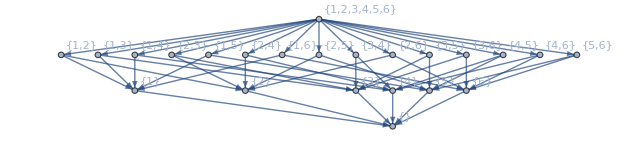

```mathematica
LatticeOfFlats@UniformMatroid[3,6]
```

#### C3Q

Determines whether a collection of sets satisfies the C3 axiom for circuits

(Note: from here on, C1, C2, and C3 will refer to sets)

Improvement: Considers all pairs of circuits C1 and C2. Is there a more efficient way?

```mathematica
C3Q[circuits_]:=Module[{C1,C2,union,possibleC3},
Catch[(*Catches the result of the function, ie whether circuits satisfies the C3 axiom*)

Do[(*Loops over possible C1 and C2 sets*)

(*Preliminaries*)
C1=circuits[[i]];
C2=circuits[[j]];
union=Union[C1,C2];
(*The only possibilities for the C3 circuit are those contained in C1 ∪ C2*)
possibleC3=Select[circuits,SubsetQ[union,#]&];

(*Check if for each x∈(C1 ∩ C2) there is an element of possibleC3 that does not contain x; ie. a valid choice for the C3 circuit*)
Do[

Catch[(*Allows for early termination of looking for said C3*)

(*Check each possible C3; we are interested in when C3 does not contain x*)
Do[
If[Not@MemberQ[C3,x],Throw[True,"x"](*Valid C3 found for this x*)]
,{C3,possibleC3}];

(*If you made it here, no valid C3 was found for this x, return False*)
Throw[False,
Echo["Failed, for"];
Echo[C1];
Echo[C2];
Echo[x];
"r"];

,"x"];
(*If you made it here, a valid C3 was found for this x*)

,{x,Intersection[C1,C2]}];
(*If you made it here, a valid C3 was found for all x's*)

,{i,1,Length@circuits},{j,i+1,Length@circuits}];
(*If you made it here, a valid C3 was found for all x's over all C1 and C2*)

(*Return True as the value of the function*)
True

,"r"]
]
```

#### B3Q

Determines whether a collection of sets satisfies the B3 axiom for bases

(Note: from here on, B1, B2, and B3 will refer to sets)
B3 is what we hope/expect the B1-x+y set to be

Improvement: Considers all pairs of bases B1 and B2. Is there a more efficient way? PluckerQ[] does some other algorithm for checking if something is a Plucker vector, which should be equivalent to this one.

```mathematica
B3Q[bases_]:=Module[{B1,B2,B3,B1sansB2,swaps,X,x,y},
Catch[(*Catches the result of the function, ie whether circuits satisfies the C3 axiom*)

Do[(*Loops over possible B1 and B2 sets*)

(*Preliminaries*)
If[i==j,Continue[]];
B1=bases[[i]];
B2=bases[[j]];
B1sansB2=Complement[B1,B2];

(*Keeps track of which x∈(B1-B2) weve found successful swaps for*)
swaps=AssociationThread[B1sansB2,False];

(*Loop over all the bases, seeing if we find a swap for each x∈(B1-B2)*)
(*If at any point we realize this is not a valid x, y swap, Continue[] the loop*)
Do[
(*First, check if B3 can be obtained from B1 with a single swap*)
(*X are the elements dropped*)
(*x is the single element dropped*)
X=Complement[B1,B3];
If[Length[X]≠1,Continue[]];
x=X[[1]];

(*If we already verified a swap for this x, keep looping*)
If[swaps[x]==True,Continue[]];

(*If the element we have to drop is in B2, it is not an x∈(B1-B2)*)
If[MemberQ[B2,x],Continue[]];

(*Find the y we have to add so that B3 = B1-x+y*)
y=Complement[B3,B1][[1]];

(*Check this y is valid, ie. y∈(B2-B1)*)
If[x≠y∧MemberQ[B2,y],
(*It is valid, so we document it*)
swaps[x]=True;
];

,{B3,bases}];

(*If any of the possible x didnt have swaps, we have failed*)
If[Not[And@@swaps],
Echo["Failed, for"];
x=Position[swaps,False][[1,1,1]];
Echo[B1];
Echo[B2];
Echo[x];
Throw[False];
];

,{i,1,Length[bases]},{j,1,Length[bases]}];

(*If you got here, there were valid swaps for all x for all B1 and B2*)
True
]
]
```

```mathematica
M=UniformMatroid[3,6];
B=M[[2]]
B3Q[B]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6},{3,5,6},{4,5,6}}

True

```mathematica
M=UniformMatroid[3,6];
B=M[[2,1;;-3]]
B3Q[B]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6}}

Failed, for

{1,5,6}

{3,4,5}

1

False

#### FQ

Checks the flat axioms

```mathematica
FQ[E_,Flats_]:=Module[{n,F1,F2,containers,coverers,partition,counts},
Catch[
(*F1*)
If[Not@MemberQ[Flats,E],
Echo["Failed F1"];
Throw[False]
];

(*F2*)
Do[
If[Not@MemberQ[Flats,Intersection@@pair],
Echo["Failed F2 for"];
Echo[pair[[1]],"F_1"];
Echo[pair[[2]],"F_2"];
Throw[False]
]
,
{pair,Subsets[Flats,{2}]}
];

(*F3*)
(*Maybe revise this to do some fancy Orderless thing like in Minimal[]*)
n=Length[E];
Do[
containers=Select[Flats,SubsetQ[#,F]&];
coverers=Minimal[Complement[containers,{F}]];
partition=Complement[#,F]&/@coverers;
counts=Tally[Join@@partition][[All,2]];
If[Length[counts]+Length[F]≠n,
Echo["Failed F3 for"];
Echo[F,"F"];
Echo["Union of F_i-F is not E-F"];
Throw[False]
];
If[Not@AllTrue[counts,#==1&],
Echo["Failed F3 for"];
Echo[F,"F"];
Echo["F_i-F have overlaps"];
Throw[False]
]
,
{F,Flats}
];

Throw[True]
]
]
```

```mathematica
classes=WedgeCongruences[UniformMatroid[3,4],2];
```

Trivial and bend 0.

Remaining set 0.183268

Ground set size 6

Number of subsets 64

Number of pairs 2016

Iterations needed 2295

Avg time per iteration 0.0000799

Loops done 1.13839

Changes done each loop {34,0}

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapsed 0.5668788

Class size | # | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

```mathematica
groundN=Subsets[Range[4],{2}];
FQ[groundN,Keys[classes]]
```

True

#### MatroidFromCircuits

Given a ground set E and a set of circuits, construct the matroid (in terms of bases).

Improvement: Is there another more efficient way to code this?
Right now, it does
1. Find all possible subsets
2. Filter out the dependent sets (ie the ones that contain circuits)
3. Find the bases

Alternative idea: maybe leverage the fact that all circuits are basic (additionally, in each of their elements) - see Gordon McNulty p. 162 Proposition 4.7 part 1

```mathematica
MatroidFromCircuits[E_,C_]:=Module[{ind,d},
(*Trivial case*)
If[C=={},Return[{E,{E}}]];

(*Find independent sets*)
ind=Table[If[AnyTrue[C,SubsetQ[subset,#]&],Nothing,subset],{subset,Subsets[E]}];

(*Bases and return*)
d=Max@@(Length/@ind);
{E,Select[ind,Length[#]==d&]}
]
```

#### Lattice

Given a set of elements, creates a lattice ordered by inclusion
1. RelationGraph[] adds edges between elements when there is proper containment
2. TransitiveReductionGraph[] removes edges that are implied by transitivity
3. Then I have to figure out the coordinates for each vertex, which is tedious, since for large graphs it prints very ugly by default

In the graph, arrows point in the direction of smaller sets

```mathematica
Lattice[elements_]:=Module[{vertices,g,layers,i,nextVertices,verticesSeen,coordinates,verticesInLayer,vertexIndex,vertex},

vertices=Sort[elements];

(*Creates the graph, but the vertices won't be in nice locations yet*)
g=TransitiveReductionGraph[
RelationGraph[SubsetQ[#1,#2]∧(#1≠#2)&,vertices],
VertexLabels->"Name"
];

(*--------------------------------------------------*)
(*Determine vertex coordinates*)
(*--------------------------------------------------*)

(*Assign vertices to layers*)
i=1;
layers={{Last[vertices]}};

(*Loop until all vertices are in a layer*)
While[True,

(*Find all vertices that are neighbors of the current layer, in a directed graph sense*)
nextVertices=Union@@(Delete[VertexOutComponent[g,#,1],1]&/@layers[[i]]);

(*If we reached the top, break the loop*)
If[nextVertices=={},Break[]];

(*Add them to the next layer*)
layers=Append[layers,nextVertices];
i++;

];

(*--------------------------------------------------*)

(*Make sure vertices only appear in a single layer, the lowest one they are in*)
verticesSeen=Last[layers];
Do[
layers[[j]]=Complement[layers[[j]],verticesSeen];
verticesSeen=Join[verticesSeen,layers[[j]]];
,{j,Length[layers]-1,1,-1}];

(*--------------------------------------------------*)

(*Assign coordinates to each vertex*)

coordinates=Table[{0,0},Length[vertices]];

Do[
verticesInLayer=Length[layers[[layerNumber]]];
Do[

vertex=layers[[layerNumber]][[vertexNumber]];
vertexIndex=Position[vertices,vertex][[1,1]];
coordinates[[vertexIndex]]={vertexNumber-verticesInLayer/2,-layerNumber};

,{vertexNumber,1,verticesInLayer}]
,{layerNumber,1,Length[layers]}];

(*--------------------------------------------------*)

(*Set the vertex coordinates*)
SetProperty[g,VertexCoordinates->coordinates]

]
```

#### MatrixWedge

Given a matrix with full row rank, the span of its rows represents a linear space. Take a wedge power of this linear space by wedging rows together.
There’s actually a Mathematica function perfect for this, but I’ll still have this method as a wrapper.

```mathematica
MatrixWedge[A_,k_]:=Minors[A,k]
```

## Tropical

The Q_M section is probably the most useful. I think I originally used many of these functions when I was figuring out the correspondence between Plücker vectors and matroids, so they may be largely obsolete

Note that all of this is over the booleans (idempotent semifield), so coefficients are either 0 or 1

### Basics

#### PluckerQ

Checks if a vector is a Plücker vector. The vector is represented by a matroid.

```mathematica
PluckerQ[M_]:=Module[{E,B,d,summation},
{E,B}=M;
d=Length[B[[1]]];
Catch[
Do[
summation=Table[
MemberQ[B,DeleteCases[A,i]]∧MemberQ[B,Union[B,{i}]]
,{i,Complement[A,B]}];
If[Count[summation,True]==1,Throw[False]]
,{A,Subsets[E,d+1]},{B,Subsets[E,d-1]}];
Throw[True]
]
]
```

### L_M

#### TropicalHyperplane

Calculates the tropical hyperplane corresponding to a Plücker vector
ie tropker(–⋀[M])

```mathematica
TropicalHyperplane[M_]:=Module[{E,B,forms,in,out},
E=First[M];

(*get the linear forms, Union[] to avoid redundant ones, Complement[] to remove the trivial one*)
forms=Complement[Union@LinearForms[M],{}];

Intersection@@Table[Tropker[E,form],{form,forms}]

]
```

#### LinearForms

Finds the linear forms corresponding to a Plücker vector (using the |J| = d+1 thing)
“Output” corresponds to whether it should echo the J that give trivial linear forms

```mathematica
LinearForms[M_,Output_:False]:=Module[{E,B,d,temp,forms},
{E,B}=M;
d=Length[B[[1]]];

(*find the linear form for each J*)
forms=Table[
temp=Table[If[MemberQ[B,DeleteCases[J,i]],i,Nothing],{i,J}];
If[Output∧Length@temp==0,Echo@J];
temp
,{J,Subsets[E,{d+1}]}];

(*remove duplicates and the trivial*)
Complement[Union[forms],{{}}]

]
```

#### Tropker

Finds the tropical kernel of a linear form. This code is pretty terse, so here’s what’s going on:

- From GG2017 p. 5 definition 2.4.1, the tropical kernel of a linear form is all elements for which dropping a single term of the element does not affect its image under the linear form.
	So if f is the linear form, it is all ∑_i a_i e_i such that for all j we have f(∑_i a_i e_i)=f(∑_(i≠j) a_i e_i)
	
- Since we are just looking over the booleans and linear forms can be represented by sets, say {1,2,4} is the linear form x_1+x_2+x_4, this amounts to finding all sets that overlap our linear form by 2 elements or not at all. These are the two cases f(∑_i a_i e_i)=1 and f(∑_i a_i e_i)=0, respectively.
	As an example, if the linear form is f={1,2,4} and we look at the element v={2,4,5} we have f(v)=1. Since when we drop a single term from v we still have nontrivial overlap with f, we will still have the quantity equal to 1. So it satisfies the above condition, and thus v∈tropker(f).
	
- So in the code, “in” is all ways of picking at least 2 terms of the linear form, “out” is all ways of picking terms not in the linear form, and the Union[] selects all elements that are either
	=0 case: do not overlap the linear form, so f(v)=0
	=1 case: overlap the linear form in at least 2 elements, so f(v)=1

```mathematica
Tropker[E_,form_]:=Module[{in,out},

(*Read what happens in the Union[], then these should make more sense*)
in=Subsets[form,{2,Length@form}];
out=Subsets[Complement[E,form]];

Union[
(*=0 case: pick from things not in the form*)
out,
(*=1 case: pick at least two things in the form*)
(Union@@#)&/@Tuples[{in,out}]
]

]
```

#### OrthogonalDual

Given a list of linear forms, find their orthogonal dual as defined in GG2017 p.11

```mathematica
OrthogonalDual[E_,forms_]:=Module[{nontrivialForms},
nontrivialForms=Complement[forms,{{}}];

If[Length[nontrivialForms]==0,

(*If there are no linear forms, it is the empty intersection (whole space)*)
Subsets[E],

(*Otherwise intersect over all tropical kernels of these linear forms*)
Intersection@@Table[Tropker[E,form],{form,nontrivialForms}]

]

]
```

#### DoubleOrthogonalDual

Does the above function twice

```mathematica
DoubleOrthogonalDual[E_,forms_]:=OrthogonalDual[E,OrthogonalDual[E,forms]]
```

### Q_M

#### QuotientModule

Generates Q_M corresponding to a Plücker vector
ie B(–⋀[M])
Uses that ℒ(M)≅Q_M, G+2 Thm. 3.3
Currently, outputs it as an association of F→{S_i} associating flats to the sets in their equivalence class

```mathematica
QuotientModule[M_]:=FlatsCongruences[M]
```

```mathematica
QuotientModule[UniformMatroid[3,6]]
```

<|{}→{{}},{1}→{{1}},{2}→{{2}},{3}→{{3}},{4}→{{4}},{5}→{{5}},{6}→{{6}},{1,2}→{{1,2}},{1,3}→{{1,3}},{1,4}→{{1,4}},{1,5}→{{1,5}},{1,6}→{{1,6}},{2,3}→{{2,3}},{2,4}→{{2,4}},{2,5}→{{2,5}},{2,6}→{{2,6}},{3,4}→{{3,4}},{3,5}→{{3,5}},{3,6}→{{3,6}},{4,5}→{{4,5}},{4,6}→{{4,6}},{5,6}→{{5,6}},{1,2,3,4,5,6}→{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,4},{1,3,5},{1,3,6},{1,4,5},{1,4,6},{1,5,6},{2,3,4},{2,3,5},{2,3,6},{2,4,5},{2,4,6},{2,5,6},{3,4,5},{3,4,6},{3,5,6},{4,5,6},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,4,5},{1,2,4,6},{1,2,5,6},{1,3,4,5},{1,3,4,6},{1,3,5,6},{1,4,5,6},{2,3,4,5},{2,3,4,6},{2,3,5,6},{2,4,5,6},{3,4,5,6},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,5,6},{1,2,4,5,6},{1,3,4,5,6},{2,3,4,5,6},{1,2,3,4,5,6}}|>

## Congruences

A set of congruence classes will be represented by an association of the from <|r_1→{s_(1,...)},...|> which associates each congruence class representative to its congruence class.

### Main

#### MatroidalQ

Checks if a pair (M,k) is matroidal, by computing congruence classes (with WedgeCongruences[] and BendCongruences[]) and then checking the flat axioms with FQ[]

```mathematica
MatroidalQ[M_,k_]:=Module[{groundM,groundN,congruenceClassRepresentatives},
(*Give an estimate for the time needed*)
(*To edit this estimate, change the function MatoridalQTimeEstimate*)
(*Echo[TimeToString@MatroidalQTimeEstimate[M,k],"ETA"];*)

(*Ground set of input matroid*)
groundM=First[M];

(*Ground set of the wedge power*)
groundN=Subsets[groundM,{k}];

congruenceClassRepresentatives=Keys@WedgeCongruences[M,k,False];

FQ[groundN,congruenceClassRepresentatives]
]
```

#### MatroidalQTimeEstimate

```mathematica
MatroidalQTimeEstimate[M_,k_]:="FIXME"
```

#### BendCongruences

Generates the congruences corresponding to a set of linear forms and a ground set E. ie. ℬ(x_1+x_2+x_3) kind of stuff.
Each form should be given as a list, ie. x_1+x_2+x_3={1,2,3}. This matches how I represent things like circuits, which can also be viewed as linear forms.

Note that this can produce the same results as QuotientModule[], but QuotientModule[] uses the isomorphism to the lattice of flats to greatly simplify things.
This function is for more general settings where a matroidal interpretation may not exist, such as ⋀^k Q_M kinds of things.

Setting the 3rd parameter to False suppresses outputs, and only returns the congruences classes as a list (no graph of the congruences is printed).

How it works: see Nicolas Bolle’s honors thesis, TCNJ 2019 under Dr. Marcus
Input: a ground set E and set of linear forms forms
Output: a list of elements r→{s_1,...} associating a representative r to its congruence class of s_i

One step that isn’t totally explained in the honor’s thesis is when it loops over pairs s_1,s_2 and merges the trees of OverBar[OverBar[s_1]+OverBar[s_2]] and OverBar[s_1+s_2]. The thinking is that we have the congruences s_1~OverBar[s_1] and s_2~OverBar[s_2] so for it to be closed as a submodule we would want the congruence s_1+s_2~OverBar[s_1]+OverBar[s_2]. But remember that when we add congruences we don’t add them directly: we merge the trees of the relevant elements. Those trees are represented by the elements OverBar[OverBar[s_1]+OverBar[s_2]] and OverBar[s_1+s_2].

```mathematica
BendCongruences[E_,forms_,debug_:True]:=Module[{t1,t2,subsets,l,reps,getRoot,bend,
s1,s2,r1,r2,noChangeCount,totalPairs,i,lastChangeIndex,lastChangePair,
classes,keys,data},

t1=AbsoluteTime[];

(*Useful variables*)
subsets=Subsets[E];
l=2^Length[E];

(*Set trivial representatives*)
reps=Association@Table[s->s,{s,subsets}];

(*Define a function to simplify things*)
getRoot[s_]:=FixedPoint[reps,s];

(*--------------------------------------------------*)

(*Set bend congruences representatives*)
(*Loop over linear forms and bends of the linear forms*)
Do[
bend=Drop[form,{i}];

If[reps[bend]==bend,

(*Case 1: the bend is in a singleton tree*)
reps[bend]=form,

(*Case 2: the bend is in a nontrivial tree*)
r1=getRoot[bend];
r2=getRoot[form];
reps[r1]=reps[r2]=Union[r1,r2]

],

{form,forms},{i,1,Length[form]}
];

(*--------------------------------------------------*)

(*Print how long the first part took*)
If[debug,
t2=AbsoluteTime[];
Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Trivial and bend relations"];
Print[];
];

(*--------------------------------------------------*)

(*Generate new congruences to close it as a submodule*)

(*So that we know when we've checked every pair*)
i=0;
noChangeCount=0;
totalPairs=Binomial[l,2];

(*Loop until the Throw[] statement exits the loop*)
Catch[
While[True,

Do[

i++;

(*The sets involved*)
s1=subsets[[i1]];
s2=subsets[[i2]];
r1=getRoot[Union[s1,s2]];
r2=getRoot[Union[getRoot[s1],getRoot[s2]]];

(*Merge trees if necessary*)
If[r1==r2,

(*If no merging was necessary*)
noChangeCount++,

(*If we need to merge trees*)
noChangeCount=0;
lastChangeIndex=i;
lastChangePair={i1,i2};

reps[r1]=reps[r2]=Union[r1,r2];

];

If[noChangeCount==totalPairs,Throw[0]],

{i1,l},{i2,i1+1,l}];

];
];

(*--------------------------------------------------*)

(*Print info about the looping over pairs*)
If[debug,
t1=t2;
t2=AbsoluteTime[];

Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Looping over pairs"];
Echo[Length[E],"Ground set size"];
Echo[l,"Number of subsets to consider"];
Echo[totalPairs,"Number of pairs to consider"];
Echo[i,"Pairs looped over"];
Echo[Round[i/(t2-t1),1],"Avg. number of pairs per second"];
Echo[lastChangeIndex,"Last change index"];
Echo[subsets[[lastChangePair]],"Last change pair"];
Print[];
];

(*--------------------------------------------------*)

(*Collapse trees into direct links to representatives*)
Do[
reps[s]=reps[reps[s]],
{s,Reverse[subsets]}
];

(*--------------------------------------------------*)

(*Print how long the tree collapse took*)
If[debug,
t1=t2;
t2=AbsoluteTime[];
Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Tree collapse"];
Print[];
];

(*--------------------------------------------------*)

(*Reverse-lookup the association*)
classes=reps//Normal//GroupBy[Last->First]//Sort;

(*--------------------------------------------------*)

(*Print how long the reverse-lookup took*)
If[debug,
t1=t2;
t2=AbsoluteTime[];
Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Reverse-lookup"];
Print[];
];

(*--------------------------------------------------*)

(*Print some info about the classes*)
If[debug,

(*For each congruence class, get {# elements, max element size, min element size}*)
keys=Keys[classes];
data=Table[class=classes[key];{Length[class],Length[key],Min[Length/@class]},{key,keys}];

(*Gather by the first element (number of elements in the class)*)
data=GatherBy[data,First];

(*For each class size, take {class size, number of classes of this size, max element size, min element size}*)
data=Table[{stats[[1,1]],Length[stats],Max[stats[[All,2]]],Min[stats[[All,3]]]},{stats,data}];

(*Print it to a table*)
Print@TableForm[Prepend[data,{"Class size","Number of classes of this size","Max elem. size","Min elem. size"}]];

Print[];
Print["Longest linear form length: ",Max[Length/@forms]];
Print[];

];

(*--------------------------------------------------*)

(*Return*)
classes

]
```

#### WedgeCongruences

Applies bend congruences for a wedge power of a matroid

Note: this would work just as well if it used PreExpectedCircuits[]. I haven’t noticed any significant differences in computation time, so I’m just using ExpectedCircuits[] since it avoids the minimality computation in PreExpectedCircuits[]. But maybe for bigger matroids there is some difference.

```mathematica
WedgeCongruences[M_,k_,output_:True]:=Module[{Cpre,wedgeE},

(*The ground set*)
wedgeE=Subsets[Ground[M],{k}];

(*The linear forms*)
Cpre=PreExpectedCircuits[M,k];

BendCongruences[wedgeE,Cpre,output]
]
```

#### WedgeLattice

Similar to WedgeCongruences, but also displays a lattice
Maybe this could be used to guess if a wedge power is matroidal, by checking if its lattice of congruence class representatives looks like a lattice of flats

```mathematica
WedgeLattice[M_,k_,output_:True]:=Module[{Cexp,wedgeE,components,representatives,CexpDD,Cwedge,Mwedge,f,levels},

(*First apply WedgeCongruences*)
components=WedgeCongruences[M,k,output];

(*Pick the representatives*)
representatives=Sort@Keys@components;

(*Print the lattice*)
Print@Lattice[representatives];
components

]
```

Trivial and bend relations 0. seconds

Looping over pairs 0.11 seconds

Ground set size 6

Number of subsets to consider 64

Number of pairs to consider 2016

Pairs looped over 2295

Avg time spent per pair 0.000046 seconds

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapse 0.34 seconds

Reverse-lookup 0.05 seconds

Class size | Number of classes of this size | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

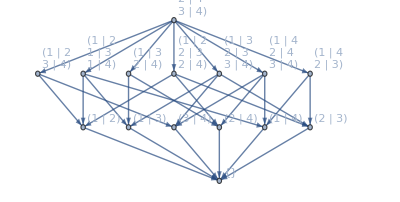

<|{}→{{}},{{1,2}}→{{{1,2}}},{{1,3}}→{{{1,3}}},{{1,4}}→{{{1,4}}},{{2,3}}→{{{2,3}}},{{2,4}}→{{{2,4}}},{{3,4}}→{{{3,4}}},{{1,2},{3,4}}→{{{1,2},{3,4}}},{{1,3},{2,4}}→{{{1,3},{2,4}}},{{1,4},{2,3}}→{{{1,4},{2,3}}},{{1,2},{1,3},{1,4}}→{{{1,2},{1,3}},{{1,2},{1,4}},{{1,3},{1,4}},{{1,2},{1,3},{1,4}}},{{1,2},{2,3},{2,4}}→{{{1,2},{2,3}},{{1,2},{2,4}},{{2,3},{2,4}},{{1,2},{2,3},{2,4}}},{{1,3},{2,3},{3,4}}→{{{1,3},{2,3}},{{1,3},{3,4}},{{2,3},{3,4}},{{1,3},{2,3},{3,4}}},{{1,4},{2,4},{3,4}}→{{{1,4},{2,4}},{{1,4},{3,4}},{{2,4},{3,4}},{{1,4},{2,4},{3,4}}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}→{{{1,2},{1,3},{2,3}},{{1,2},{1,3},{2,4}},{{1,2},{1,3},{3,4}},{{1,2},{1,4},{2,3}},{{1,2},{1,4},{2,4}},{{1,2},{1,4},{3,4}},{{1,2},{2,3},{3,4}},{{1,2},{2,4},{3,4}},{{1,3},{1,4},{2,3}},{{1,3},{1,4},{2,4}},{{1,3},{1,4},{3,4}},{{1,3},{2,3},{2,4}},{{1,3},{2,4},{3,4}},{{1,4},{2,3},{2,4}},{{1,4},{2,3},{3,4}},{{2,3},{2,4},{3,4}},{{1,2},{1,3},{1,4},{2,3}},{{1,2},{1,3},{1,4},{2,4}},{{1,2},{1,3},{1,4},{3,4}},{{1,2},{1,3},{2,3},{2,4}},{{1,2},{1,3},{2,3},{3,4}},{{1,2},{1,3},{2,4},{3,4}},{{1,2},{1,4},{2,3},{2,4}},{{1,2},{1,4},{2,3},{3,4}},{{1,2},{1,4},{2,4},{3,4}},{{1,2},{2,3},{2,4},{3,4}},{{1,3},{1,4},{2,3},{2,4}},{{1,3},{1,4},{2,3},{3,4}},{{1,3},{1,4},{2,4},{3,4}},{{1,3},{2,3},{2,4},{3,4}},{{1,4},{2,3},{2,4},{3,4}},{{1,2},{1,3},{1,4},{2,3},{2,4}},{{1,2},{1,3},{1,4},{2,3},{3,4}},{{1,2},{1,3},{1,4},{2,4},{3,4}},{{1,2},{1,3},{2,3},{2,4},{3,4}},{{1,2},{1,4},{2,3},{2,4},{3,4}},{{1,3},{1,4},{2,3},{2,4},{3,4}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}}|>

```mathematica
WedgeLattice[UniformMatroid[3,4],2]
```

#### VisualizeCongruences

Prints two graphs visualizing a set of congruence classes

```mathematica
VisualizeCongruences[classes_]:=Module[{reps,E,edges},

(*One that connects congruence classes*)
reps=Keys[classes];
E=Last[reps];
edges=Table[
child->rep,{rep,reps},
{child,Complement[classes[rep],{rep}]}
];
edges=Flatten[edges,1];

Print@Graph[Subsets[E],edges,VertexLabels->Automatic];

(*And one for the lattice*)
Print@Lattice@reps

]
```

```mathematica
classes=WedgeCongruences[UniformMatroid[3,4],2];
```

Trivial and bend 0.

Remaining set 0.0933482

Ground set size 6

Number of subsets 64

Number of pairs 2016

Iterations needed 2295

Avg time per iteration 0.0000407

Loops done 1.13839

Changes done each loop {34,0}

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapsed 0.423895

Class size | # | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

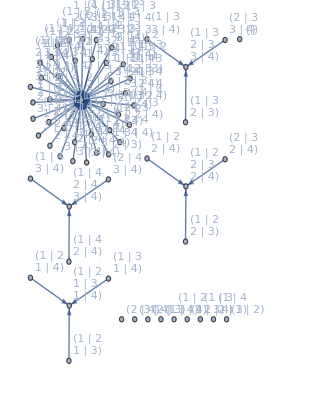

-Graphics-

```mathematica
VisualizeCongruences[classes]
```

### Conj

Stands for “conjecture”, because all of these rely on the conjecture that we only need to run BendCongruences[] on elements with |s_1|≤1.
They are all identical, except they use the Conj versions of each other and BendCongruencesConj[] looks at waaay fewer pairs than BendCongruences[].

#### MatroidalQConj

Checks if a pair (M,k) is matroidal, by computing congruence classes (with WedgeCongruences[] and BendCongruences[]) and then checking the flat axioms with FQ[]

```mathematica
MatroidalQConj[M_,k_]:=Module[{groundM,groundN,congruenceClassRepresentatives},
(*Give an estimate for the time needed*)
(*To edit this estimate, change the function MatoridalQTimeEstimate*)
(*Echo[TimeToString@MatroidalQTimeEstimate[M,k],"ETA"];*)

(*Ground set of input matroid*)
groundM=First[M];

(*Ground set of the wedge power*)
groundN=Subsets[groundM,{k}];

congruenceClassRepresentatives=Keys@WedgeCongruencesConj[M,k,False];

FQ[groundN,congruenceClassRepresentatives]
]
```

#### BendCongruencesConj

```mathematica
BendCongruencesConj[E_,forms_,debug_:True]:=Module[{t1,t2,subsets,m,reps,getRoot,bend,
s1,s2,r1,r2,totalPairs,i,lastChangeIndex,lastChangePair,
classes,keys,data},

t1=AbsoluteTime[];

(*Useful variables*)
subsets=Subsets[E];
m=Length[E];

(*Set trivial representatives*)
reps=Association@Table[s->s,{s,subsets}];

(*Define a function to simplify things*)
getRoot[s_]:=FixedPoint[reps,s];

(*--------------------------------------------------*)

(*Set bend congruences representatives*)
(*Loop over linear forms and bends of the linear forms*)
Do[
bend=Drop[form,{i}];

If[reps[bend]==bend,

(*Case 1: the bend is in a singleton tree*)
reps[bend]=form,

(*Case 2: the bend is in a nontrivial tree*)
r1=getRoot[bend];
r2=getRoot[form];
reps[r1]=reps[r2]=Union[r1,r2]

],

{form,forms},{i,1,Length[form]}
];

(*--------------------------------------------------*)

(*Print how long the first part took*)
If[debug,
t2=AbsoluteTime[];
Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Trivial and bend relations"];
Print[];
];

(*--------------------------------------------------*)

(*Generate new congruences to close it as a submodule*)

(*Keeps track of which number pair we're on*)
i=0;

(*No looping needed since we're just checking all pairs with |Subscript[s, 1]|≤1*)
Do[

i++;

(*The sets involved*)
s1=subsets[[i1]];
s2=subsets[[i2]];
r1=getRoot[Union[s1,s2]];
r2=getRoot[Union[getRoot[s1],getRoot[s2]]];

(*Merge trees if necessary*)
If[r1==r2,,

(*If we need to merge trees*)
lastChangeIndex=i;
lastChangePair={i1,i2};

reps[r1]=reps[r2]=Union[r1,r2];

],

{i1,1,1+m},{i2,i1+1,2^m}];

(*--------------------------------------------------*)

(*Total number of pairs looped over*)
(*My number for this in the honor's thesis was wrong by about m^2, but the m2^m order is still right*)
totalPairs=2^m-1+m(2^m-m-1)+Binomial[m,2];

(*Print info about the looping over pairs*)
If[debug,
t1=t2;
t2=AbsoluteTime[];

Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Looping over pairs"];
Echo[m,"Ground set size"];
Echo[2^m,"Number of subsets to consider"];
Echo[totalPairs,"Number of pairs considered"];
Echo[Round[totalPairs/(t2-t1),1],"Avg. number of pairs per second"];
Echo[lastChangeIndex,"Last change index"];
Echo[subsets[[lastChangePair]],"Last change pair"];
Print[];
];

(*--------------------------------------------------*)

(*Collapse trees into direct links to representatives*)
Do[
reps[s]=reps[reps[s]],
{s,Reverse[subsets]}
];

(*--------------------------------------------------*)

(*Print how long the tree collapse took*)
If[debug,
t1=t2;
t2=AbsoluteTime[];
Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Tree collapse"];
Print[];
];

(*--------------------------------------------------*)

(*Reverse-lookup the association*)
classes=reps//Normal//GroupBy[Last->First]//Sort;

(*--------------------------------------------------*)

(*Print how long the reverse-lookup took*)
If[debug,
t1=t2;
t2=AbsoluteTime[];
Echo[ToString[Round[t2-t1,0.01]]<>" seconds","Reverse-lookup"];
Print[];
];

(*--------------------------------------------------*)

(*Print some info about the classes*)
If[debug,

(*For each congruence class, get {# elements, max element size, min element size}*)
keys=Keys[classes];
data=Table[class=classes[key];{Length[class],Length[key],Min[Length/@class]},{key,keys}];

(*Gather by the first element (number of elements in the class)*)
data=GatherBy[data,First];

(*For each class size, take {class size, number of classes of this size, max element size, min element size}*)
data=Table[{stats[[1,1]],Length[stats],Max[stats[[All,2]]],Min[stats[[All,3]]]},{stats,data}];

(*Print it to a table*)
Print@TableForm[Prepend[data,{"Class size","Number of classes of this size","Max elem. size","Min elem. size"}]];

Print[];
Print["Longest linear form length: ",Max[Length/@forms]];
Print[];

];

(*--------------------------------------------------*)

(*Return*)
classes

]
```

Verification that this agrees with BendCongruences for U_(3,4) ,k=2:

```mathematica
M=UniformMatroid[3,4];
```

```mathematica
classes=WedgeCongruences[M,2];
```

Trivial and bend relations 0. seconds

Looping over pairs 0.1 seconds

Ground set size 6

Number of subsets to consider 64

Number of pairs to consider 2016

Pairs looped over 2295

Avg. number of pairs per second 23716

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapse 0.33 seconds

Reverse-lookup 0.05 seconds

Class size | Number of classes of this size | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

```mathematica
classesConjecture=WedgeCongruencesConj[M,2];
```

Trivial and bend relations 0. seconds

Looping over pairs 0.05 seconds

Ground set size 6

Number of subsets to consider 64

Number of pairs considered 420

Avg. number of pairs per second 7798

Last change index 279

Last change pair {{{2,3}},{{1,3},{2,4},{3,4}}}

Tree collapse 0.29 seconds

Reverse-lookup 0.05 seconds

Class size | Number of classes of this size | Max elem. size | Min elem. size
1 | 10 | 2 | 0
4 | 4 | 3 | 2
38 | 1 | 6 | 3

Longest linear form length: 3

```mathematica
classes==classesConjecture
```

True

#### WedgeCongruencesConj

Applies bend congruences for a wedge power of a matroid

```mathematica
WedgeCongruencesConj[M_,k_,output_:True]:=Module[{Cpre,wedgeE},

(*The ground set*)
wedgeE=Subsets[Ground[M],{k}];

(*The linear forms*)
Cpre=PreExpectedCircuits[M,k];

BendCongruencesConj[wedgeE,Cpre,output]
]
```

#### WedgeLatticeConj

Similar to WedgeCongruences, but also displays a lattice
If Cwedge satisfies C3, orders the lattice by rank
	Otherwise, does it by length

```mathematica
WedgeLatticeConj[M_,k_,output_:True]:=Module[{Cexp,wedgeE,components,representatives,CexpDD,Cwedge,Mwedge,f,levels},

(*First apply WedgeCongruences*)
components=WedgeCongruencesConj[M,k,output];

(*Pick the representatives*)
representatives=Sort@Keys@components;

(*Print the lattice*)
Print@Lattice[representatives];
components

]
```

28 Set initial congruences from bend relations and self-congruences

226 Closed as a submodule, needs closing as an equivalence relation

226 Closed as both a submodule and equivalence relation

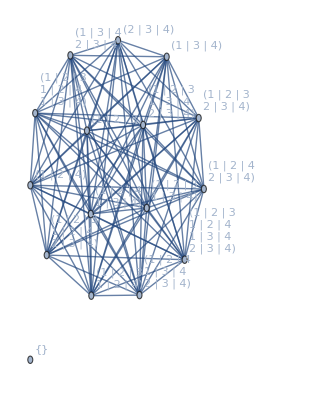

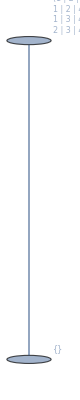

<|{}→{{}},{{1,2,3},{1,2,4},{1,3,4},{2,3,4}}→{{{1,2,3},{1,2,4}},{{1,2,3}},{{1,2,4}},{{1,3,4}},{{2,3,4}},{{1,2,3},{1,3,4}},{{1,2,3},{2,3,4}},{{1,2,4},{1,3,4}},{{1,2,4},{2,3,4}},{{1,3,4},{2,3,4}},{{1,2,3},{1,2,4},{1,3,4}},{{1,2,3},{1,2,4},{2,3,4}},{{1,2,3},{1,3,4},{2,3,4}},{{1,2,4},{1,3,4},{2,3,4}},{{1,2,3},{1,2,4},{1,3,4},{2,3,4}}}|>

```mathematica
WedgeLattice[UniformMatroid[3,4],3]
```

## Expected Circuits

### Construction

#### PreExpectedCircuits

The first set I generate, of just wedging circuits with additional elements

```mathematica
PreExpectedCircuits[M_,k_]:=Module[{subsets,circuits,nonzero,return},
subsets=Subsets[First[M],{k-1}];
circuits=Circuits[M];

return=Table[
Union[I,{elem}]
,{circuit,circuits},{I,subsets},{elem,Complement[circuit,I]}];

Union@Flatten[return,1]

]
```

#### ExpectedCircuits

The minimal elements of the pre expected circuits

```mathematica
ExpectedCircuits[M_,k_]:=Minimal[Complement[PreExpectedCircuits[M,k],{{}}]]
```

#### WedgeCircuits

Improvements: optimize this in some way??? Orthogonal duals seem like they should be very expensive.

The code for DoubleOrthogonalDual[] is in Tropical→L_M

Takes the double orthogonal dual, removes the trivial element, and selects minimal elements.

```mathematica
WedgeCircuits[M_,k_]:=Minimal[
Complement[
DoubleOrthogonalDual[Subsets[Ground[M],{k}],ExpectedCircuits[M,k]]
,{{}}
]
]
```

### Misc

#### CircuitCompletion???

Given some collection Cexp (or more generally, any collection of subsets of a ground set that satisfy C1 and C2 axioms), adds additional elements to make it into a set of circuits
No clue if this is even possible

```mathematica
CircuitCompletion[Cexp_]:=Module[{},

]
```

### Congruences Proof

No longer needed, since I finished the proof that C_exp generates the same congruences as C_pre, using these functions to help understand the various cases

#### CoverQ

Checks if the sets in SubCollection “cover” the sets in Collection; ie if every element of Collection can be expressed as a union of elements of SubCollection

```mathematica
CoverQ[SubCollection_,Collection_]:=Module[{collection,subsets},

(*remove the trivial cases of a union of a single element*)
collection=Complement[Collection,SubCollection];

Catch[

(*check the covering condition for each element in the collection*)
Do[
(*if it isn't covered, Echo[] the counterexample and exit*)
(*regular == should be fine since I everything is ordered correctly, ie. won't be comparing {1,2} to {2,1} and getting False*)
If[Not[Union@@Select[SubCollection,SubsetQ[set,#]&]==set],Echo[set,"Fails for"];Throw[False]]
,{set,collection}];

Throw[True]
]

]
```

#### ExpectedCircuitsCoverQ

Like CoverQ but takes the matroid and k, and first generates the pre expected circuits and expected circuits, and see if they cover.
Saves the step of regenerating C_pre to find C_exp.

```mathematica
ExpectedCircuitsCoverQ[M_,k_]:=Module[{pre,exp},
pre=PreExpectedCircuits[M,k];
exp=Minimal[Select[pre,#≠{}&]];
CoverQ[exp,pre]
]
```

## Useful

## Matroids

How to import the data from http://www-imai.is.s.u-tokyo.ac.jp/~ymatsu/matroid/ to our format
Must format their data as a .txt file that looks like:

#### Data file format

Some text in the beginning where I can describe
what’s in this file
etc. etc.

START

2 1
**
0*

3 1
***
0**
00*

n d
Matroid codes

#### Get matroids

Pick data file

```mathematica
f=SystemDialogInput["FileOpen"];
```

Load and interpret data

```mathematica
(*Read in file*)
matroidCodes=ReadList[f,String];

(*Remove everything before START*)
i=Position[matroidCodes,"START"][[1,1]];
matroidCodes=Drop[matroidCodes,i];

(*Split at the n,d*)
codesList=SplitBy[matroidCodes,StringContainsQ[#,"*"]&];

(*Interpret the codes, and form an association "matroids"*)
(*Elements are {n,d}->{list of matroids with those n,d}*)
matroids=Association@Table[
{n,d}=ToExpression@StringSplit[codesList[[2i-1,1]]];
rawCodes=codesList[[2i]];

groundSet=Range[n];
subsets=Reverse@Subsets[groundSet,{d}];

codedBases=ToCharacterCode@rawCodes;
l=Length[First[codedBases]];
decodedBases=Reverse/@Table[If[bases[[i]]==42,subsets[[i]],Nothing],{bases,codedBases},{i,1,l}];
Ms=Transpose@{Table[groundSet,Length[decodedBases]],decodedBases};

{n,d}->Ms

,{i,1,Length[codesList]/2}];
```

Check B3 axiom
May take a while, don’t need to do this if you trust the data file and code

```mathematica
Ms=Flatten[Values[matroids],1];
B3Q[Last[#]]&/@Ms;
```

#### Save matroids

```mathematica
f=SystemDialogInput["FileSave"];
Export[f,matroids]
```

C:\Users\Nick\Documents\Undergrad\Labs\Marcus\Data\matroids.txt

#### Load matroids

```mathematica
f=SystemDialogInput["FileOpen"];
matroids=ToExpression@Import[f]
```

#### Alternative format

If you don’t really care about the {n,d} of the matroids, you can do the following to just obtain a list of the matroids

```mathematica
matroidsList=Flatten[Values[matroids],1]
```

## Work

## 1/20/20

### Testing the new Lattice[]

```mathematica
classes=ToExpression@Import[SystemDialogInput["FileOpen"]];
```

```mathematica
vertices=Keys[classes]
```

{{},{{1,2}},{{1,3}},{{1,4}},{{1,5}},{{1,6}},{{2,3}},{{2,4}},{{2,5}},{{2,6}},{{3,4}},{{3,5}},{{3,6}},{{4,5}},{{4,6}},{{5,6}},{{1,2},{3,4}},{{1,2},{3,5}},{{1,2},{3,6}},{{1,2},{4,5}},{{1,2},{4,6}},{{1,2},{5,6}},{{1,3},{2,4}},{{1,3},{2,5}},{{1,3},{2,6}},{{1,3},{4,5}},{{1,3},{4,6}},{{1,3},{5,6}},{{1,4},{2,3}},{{1,4},{2,5}},{{1,4},{2,6}},{{1,4},{3,5}},{{1,4},{3,6}},{{1,4},{5,6}},{{1,5},{2,3}},{{1,5},{2,4}},{{1,5},{2,6}},{{1,5},{3,4}},{{1,5},{3,6}},{{1,5},{4,6}},{{1,6},{2,3}},{{1,6},{2,4}},{{1,6},{2,5}},{{1,6},{3,4}},{{1,6},{3,5}},{{1,6},{4,5}},{{2,3},{4,5}},{{2,3},{4,6}},{{2,3},{5,6}},{{2,4},{3,5}},{{2,4},{3,6}},{{2,4},{5,6}},{{2,5},{3,4}},{{2,5},{3,6}},{{2,5},{4,6}},{{2,6},{3,4}},{{2,6},{3,5}},{{2,6},{4,5}},{{3,4},{5,6}},{{3,5},{4,6}},{{3,6},{4,5}},{{1,2},{3,4},{5,6}},{{1,2},{3,5},{4,6}},{{1,2},{3,6},{4,5}},{{1,3},{2,4},{5,6}},{{1,3},{2,5},{4,6}},{{1,3},{2,6},{4,5}},{{1,4},{2,3},{5,6}},{{1,4},{2,5},{3,6}},{{1,4},{2,6},{3,5}},{{1,5},{2,3},{4,6}},{{1,5},{2,4},{3,6}},{{1,5},{2,6},{3,4}},{{1,6},{2,3},{4,5}},{{1,6},{2,4},{3,5}},{{1,6},{2,5},{3,4}},{{1,2},{1,3},{1,4},{1,5},{1,6}},{{1,2},{2,3},{2,4},{2,5},{2,6}},{{1,3},{2,3},{3,4},{3,5},{3,6}},{{1,4},{2,4},{3,4},{4,5},{4,6}},{{1,5},{2,5},{3,5},{4,5},{5,6}},{{1,6},{2,6},{3,6},{4,6},{5,6}},{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}}

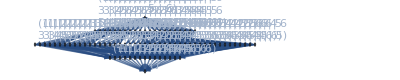

```mathematica
g=Lattice[vertices]
```

### C_wedge for U_(3,6), k=2

```mathematica
M=UniformMatroid[3,6];
k=2;
```

```mathematica
Cwedge=WedgeCircuits[M,k]
```

{{{1,2},{1,3},{1,4}},{{1,2},{1,3},{1,5}},{{1,2},{1,3},{1,6}},{{1,2},{1,4},{1,5}},{{1,2},{1,4},{1,6}},{{1,2},{1,5},{1,6}},{{1,2},{2,3},{2,4}},{{1,2},{2,3},{2,5}},{{1,2},{2,3},{2,6}},{{1,2},{2,4},{2,5}},{{1,2},{2,4},{2,6}},{{1,2},{2,5},{2,6}},{{1,3},{1,4},{1,5}},590,{{2,5},{3,5},{3,6},{4,6}},{{2,5},{3,6},{4,5},{4,6}},{{2,6},{3,4},{3,5},{4,5}},{{2,6},{3,4},{3,5},{4,6}},{{2,6},{3,4},{3,5},{5,6}},{{2,6},{3,4},{3,6},{4,5}},{{2,6},{3,4},{4,5},{5,6}},{{2,6},{3,5},{3,6},{4,5}},{{2,6},{3,5},{4,5},{4,6}},{{3,4},{3,5},{4,6},{5,6}},{{3,4},{3,6},{4,5},{5,6}},{{3,5},{3,6},{4,5},{4,6}}}
 |  |  |  |

```mathematica
Cexp=ExpectedCircuits[M,k]
```

{{{1,2},{1,3},{1,4}},{{1,2},{1,3},{1,5}},{{1,2},{1,3},{1,6}},{{1,2},{1,4},{1,5}},{{1,2},{1,4},{1,6}},{{1,2},{1,5},{1,6}},{{1,2},{2,3},{2,4}},{{1,2},{2,3},{2,5}},{{1,2},{2,3},{2,6}},{{1,2},{2,4},{2,5}},{{1,2},{2,4},{2,6}},{{1,2},{2,5},{2,6}},{{1,3},{1,4},{1,5}},{{1,3},{1,4},{1,6}},{{1,3},{1,5},{1,6}},{{1,3},{2,3},{3,4}},{{1,3},{2,3},{3,5}},{{1,3},{2,3},{3,6}},{{1,3},{3,4},{3,5}},{{1,3},{3,4},{3,6}},{{1,3},{3,5},{3,6}},{{1,4},{1,5},{1,6}},{{1,4},{2,4},{3,4}},{{1,4},{2,4},{4,5}},{{1,4},{2,4},{4,6}},{{1,4},{3,4},{4,5}},{{1,4},{3,4},{4,6}},{{1,4},{4,5},{4,6}},{{1,5},{2,5},{3,5}},{{1,5},{2,5},{4,5}},{{1,5},{2,5},{5,6}},{{1,5},{3,5},{4,5}},{{1,5},{3,5},{5,6}},{{1,5},{4,5},{5,6}},{{1,6},{2,6},{3,6}},{{1,6},{2,6},{4,6}},{{1,6},{2,6},{5,6}},{{1,6},{3,6},{4,6}},{{1,6},{3,6},{5,6}},{{1,6},{4,6},{5,6}},{{2,3},{2,4},{2,5}},{{2,3},{2,4},{2,6}},{{2,3},{2,5},{2,6}},{{2,3},{3,4},{3,5}},{{2,3},{3,4},{3,6}},{{2,3},{3,5},{3,6}},{{2,4},{2,5},{2,6}},{{2,4},{3,4},{4,5}},{{2,4},{3,4},{4,6}},{{2,4},{4,5},{4,6}},{{2,5},{3,5},{4,5}},{{2,5},{3,5},{5,6}},{{2,5},{4,5},{5,6}},{{2,6},{3,6},{4,6}},{{2,6},{3,6},{5,6}},{{2,6},{4,6},{5,6}},{{3,4},{3,5},{3,6}},{{3,4},{4,5},{4,6}},{{3,5},{4,5},{5,6}},{{3,6},{4,6},{5,6}}}

```mathematica
Length[Cwedge]
Length[Cexp]
```

615

60

C_wedge ran surprisingly quickly. I figured it would be running until after heat death of the universe, but it finished in under a minute.
Clearly they’re not equal. Does C_wedge satisfy the circuit axioms? Do they generate the same congruences?

```mathematica
C3Q[Cwedge]
```

Failed, for

{{1,2},{1,3},{1,4}}

{{1,2},{1,3},{2,3},{5,6}}

{1,2}

False

Fails the circuit axioms. This sucks.